```mathematica
DInt[ρ_]:=1/ρ-(1+1/ρ)ⅇ^(-2ρ)
```

```mathematica
XInt[ρ_]:=(1+ρ)ⅇ^-ρ
```

```mathematica
IInt[ρ_]:=ⅇ^-ρ(1+ρ+1/3 ρ^2)
```

```mathematica
D2Int[ρ_]:=1/ρ-ⅇ^(-2ρ)(1/6 ρ^2+3/4 ρ+11/8+1/ρ)
```

```mathematica
X2Int[ρ_]:=1/5(ⅇ^(-2ρ)(25/8-23/4 ρ-3 ρ^2-1/3 ρ^3)+6/ρ(IInt[ρ]^2(EulerGamma+Log[ρ])+IInt[-ρ]^2 ExpIntegralEi[-4ρ]-2IInt[ρ]IInt[-ρ] ExpIntegralEi[-2ρ]))
```

```mathematica
H[ρm_,ρ_]:=-2(1-1/ρ+(2DInt[ρ]-D2Int[ρ]+ρm(2IInt[ρ]XInt[ρ]-X2Int[ρ]))/(1+ρm IInt[ρ]^2))
```

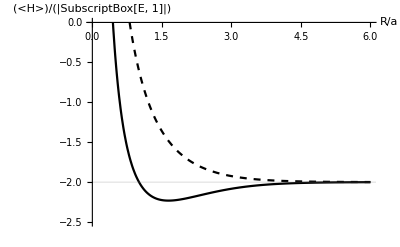

```mathematica
Plot[{H[1,ρ],H[-1,ρ]},{ρ,0,6},PlotRange->{-2.5,0},AxesLabel->{"R/a","(<H>)/(|SubscriptBox[E, 1]|)"},PlotStyle->{{Black},{Black,Dashed}},GridLines->{None,{-2}}]
```

```mathematica
Kinetic[ρm_,ρ_]:=-2(1-2((1+ρm IInt[ρ]XInt[ρ])/(1+ρm IInt[ρ]^2)))
```

```mathematica
IonPotential[ρm_,ρ_]:=-4((1+DInt[ρ]+2ρm IInt[ρ]XInt[ρ])/(1+ρm IInt[ρ]^2))
```

```mathematica
ElectronPotential[ρm_,ρ_]:=2((D2Int[ρ]+ρm X2Int[ρ])/(1+ρm IInt[ρ]^2))
```

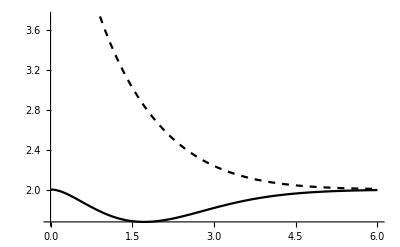

```mathematica
Plot[{Kinetic[1,ρ],Kinetic[-1,ρ]},{ρ,0,6},PlotStyle->{{Black},{Black,Dashed}}]
```

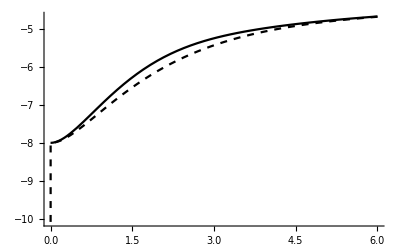

```mathematica
Plot[{IonPotential[1,ρ],IonPotential[-1,ρ]},{ρ,0,6},PlotStyle->{{Black},{Black,Dashed}}]
```

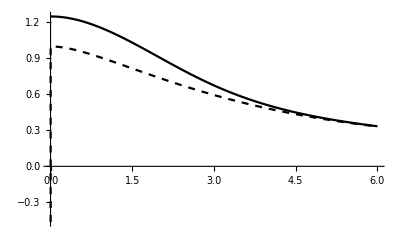

```mathematica
Plot[{ElectronPotential[1,ρ],ElectronPotential[-1,ρ]},{ρ,0,6},PlotStyle->{{Black},{Black,Dashed}}]
```